```mathematica
Parametric Analysis of second order systems with closed loop 
of linear differential equations
```

```mathematica
Given a generic second order system with closed loop of the form:
Ẋ = AX + Bu 
where "A" is called the characteristic matrix of the system of the form:
A=[{{a, b}, {c, d}}], Ẋ and X are vectors of 1x 2, B = [{{h}, {k}}] and u = [{{Subscript[x, 1], 0}}].  Solving "AX + Bu" we get:
Ẋ = [{{a + h, b}, {c + k, d}}]X;  Then we calculate eigenvalues with:
Det(A - λI ) =λ^2 - (a+h+d) λ + ((a+h)*d - b*(c + k)), finally we have, Subscript[λ, 1,2]=(a+h+d)/2±(√((a+h+d)^2-4((a+h)*d-b*(c+k))))/2, in order to Analize second order system we must consider following cases:
```

Spiral Sink ((a+h)+d)^2-4((a+h)*d-b*(c + k)) < 0 and ((a +h) +d) < 0

```mathematica
Reduce[((a+h)+d)^2 - 4((a+h)*d-b*(c+k))<0 &&((a+h)+d)<0,{a,b,c, h,k,d}, Reals]
```

(b<0&&((h<-a&&((-c<k<(-a^2-b c-2 a h-h^2)/b&&a+h-2 √(-b c-b k)<d<a+h+2 √(-b c-b k))||(k≥(-a^2-b c-2 a h-h^2)/b&&a+h-2 √(-b c-b k)<d<-a-h)))||(h≥-a&&k>(-a^2-b c-2 a h-h^2)/b&&a+h-2 √(-b c-b k)<d<-a-h)))||(b>0&&((h<-a&&((k≤(-a^2-b c-2 a h-h^2)/b&&a+h-2 √(-b c-b k)<d<-a-h)||((-a^2-b c-2 a h-h^2)/b<k<-c&&a+h-2 √(-b c-b k)<d<a+h+2 √(-b c-b k))))||(h≥-a&&k<(-a^2-b c-2 a h-h^2)/b&&a+h-2 √(-b c-b k)<d<-a-h)))

Nodal Sink ((a+h)+d)^2-4((a+h)*d-b*(c+k)) > 0 and (λ_1)(λ_2) > 0 and (λ_1)+(λ_2)<0

```mathematica
Reduce[((a+h)+d)^2 - 4((a+h)*d-b*(c+k))>0 && (((a+h) +d)/2 + Sqrt[((a+h)+d)^2 - 4((a+h)*d-b*(c+k))]/2) * (((a+h) +d)/2 - Sqrt[((a+h)+d)^2 - 4((a+h)*d-b*(c+k))]/2) > 0 && (((a+h) +d)/2 + Sqrt[((a+h)+d)^2 - 4((a+h)*d-b*(c+k))]/2) + (((a+h) +d)/2 - Sqrt[((a+h)+d)^2 - 4((a+h)*d-b*(c+k))]/2) < 0,{a,b,c, h, k,d}, Reals]
```

(b<0&&((h<-a&&((k<-c&&d<(b c+b k)/(a+h))||(k==-c&&(d<a+h+2 √(-b c-b k)||a+h+2 √(-b c-b k)<d<(b c+b k)/(a+h)))||(-c<k<(-a^2-b c-2 a h-h^2)/b&&(d<a+h-2 √(-b c-b k)||a+h+2 √(-b c-b k)<d<(b c+b k)/(a+h)))||(k≥(-a^2-b c-2 a h-h^2)/b&&d<a+h-2 √(-b c-b k))))||(h==-a&&k>-c&&d<a+h-2 √(-b c-b k))||(h>-a&&k>(-a^2-b c-2 a h-h^2)/b&&(b c+b k)/(a+h)<d<a+h-2 √(-b c-b k))))||(b==0&&h<-a&&(d<a+h||a+h<d<0))||(b>0&&((h<-a&&((k≤(-a^2-b c-2 a h-h^2)/b&&d<a+h-2 √(-b c-b k))||((-a^2-b c-2 a h-h^2)/b<k<-c&&(d<a+h-2 √(-b c-b k)||a+h+2 √(-b c-b k)<d<(b c+b k)/(a+h)))||(k==-c&&(d<a+h+2 √(-b c-b k)||a+h+2 √(-b c-b k)<d<(b c+b k)/(a+h)))||(k>-c&&d<(b c+b k)/(a+h))))||(h==-a&&k<-c&&d<a+h-2 √(-b c-b k))||(h>-a&&k<(-a^2-b c-2 a h-h^2)/b&&(b c+b k)/(a+h)<d<a+h-2 √(-b c-b k))))

Spiral Source ((a+h)+d)^2-4((a+h)*d-b*(c+k)) < 0 and ((a+h)+d) > 0

```mathematica
Reduce[((a+h)+d)^2 - 4((a+h)*d-b*(c+k))<0 &&  ((a+h)+ d) > 0,{a,b,c,h,k,d}, Reals]
```

(b<0&&((h≤-a&&k>(-a^2-b c-2 a h-h^2)/b&&-a-h<d<a+h+2 √(-b c-b k))||(h>-a&&((-c<k<(-a^2-b c-2 a h-h^2)/b&&a+h-2 √(-b c-b k)<d<a+h+2 √(-b c-b k))||(k≥(-a^2-b c-2 a h-h^2)/b&&-a-h<d<a+h+2 √(-b c-b k))))))||(b>0&&((h≤-a&&k<(-a^2-b c-2 a h-h^2)/b&&-a-h<d<a+h+2 √(-b c-b k))||(h>-a&&((k≤(-a^2-b c-2 a h-h^2)/b&&-a-h<d<a+h+2 √(-b c-b k))||((-a^2-b c-2 a h-h^2)/b<k<-c&&a+h-2 √(-b c-b k)<d<a+h+2 √(-b c-b k))))))

Nodal Source ((a+h)+d)^2-4((a+h)*d-b*(c+k)) > 0 and (λ_1)(λ_2) > 0 and (λ_1)+(λ_2)>0

```mathematica
Reduce[((a+h)+d)^2 - 4((a+h)*d-b*(c+k))>0 && (((a+h) +d)/2 + Sqrt[((a+h)+d)^2 - 4((a+h)*d-b*(c+k))]/2) * (((a+h) +d)/2 - Sqrt[((a+h)+d)^2 - 4((a+h)*d-b*(c+k))]/2) > 0 && (((a+h) +d)/2 + Sqrt[((a+h)+d)^2 - 4((a+h)*d-b*(c+k))]/2) + (((a+h) +d)/2 - Sqrt[((a+h)+d)^2 - 4((a+h)*d-b*(c+k))]/2) > 0,{a,b,c,h,k,d}, Reals]
```

(b<0&&((h<-a&&k>(-a^2-b c-2 a h-h^2)/b&&a+h+2 √(-b c-b k)<d<(b c+b k)/(a+h))||(h==-a&&k>-c&&d>a+h+2 √(-b c-b k))||(h>-a&&((k<-c&&d>(b c+b k)/(a+h))||(k==-c&&((b c+b k)/(a+h)<d<a+h+2 √(-b c-b k)||d>a+h+2 √(-b c-b k)))||(-c<k<(-a^2-b c-2 a h-h^2)/b&&((b c+b k)/(a+h)<d<a+h-2 √(-b c-b k)||d>a+h+2 √(-b c-b k)))||(k≥(-a^2-b c-2 a h-h^2)/b&&d>a+h+2 √(-b c-b k))))))||(b==0&&h>-a&&(0<d<a+h||d>a+h))||(b>0&&((h<-a&&k<(-a^2-b c-2 a h-h^2)/b&&a+h+2 √(-b c-b k)<d<(b c+b k)/(a+h))||(h==-a&&k<-c&&d>a+h+2 √(-b c-b k))||(h>-a&&((k≤(-a^2-b c-2 a h-h^2)/b&&d>a+h+2 √(-b c-b k))||((-a^2-b c-2 a h-h^2)/b<k<-c&&((b c+b k)/(a+h)<d<a+h-2 √(-b c-b k)||d>a+h+2 √(-b c-b k)))||(k==-c&&((b c+b k)/(a+h)<d<a+h+2 √(-b c-b k)||d>a+h+2 √(-b c-b k)))||(k>-c&&d>(b c+b k)/(a+h))))))

Saddle ((a+h)+d)^2-4((a+h)*d-b*(c+k)) > 0 and (λ_1)(λ_2) < 0

```mathematica
Reduce[((a+h)+d)^2 - 4((a+h)*d-b*(c+k))>0 && (((a+h) +d)/2 + Sqrt[((a+h)+d)^2 - 4((a+h)*d-b*(c+k))]/2) * (((a+h) +d)/2 - Sqrt[((a+h)+d)^2 - 4((a+h)*d-b*(c+k))]/2) < 0 ,{a,b,c,h,k,d}, Reals]
```

(b<0&&((h<-a&&((k<(-a^2-b c-2 a h-h^2)/b&&d>(b c+b k)/(a+h))||(k==(-a^2-b c-2 a h-h^2)/b&&d>a+h+2 √(-b c-b k))||(k>(-a^2-b c-2 a h-h^2)/b&&d>(b c+b k)/(a+h))))||(h==-a&&k<-c)||(h>-a&&((k<(-a^2-b c-2 a h-h^2)/b&&d<(b c+b k)/(a+h))||(k==(-a^2-b c-2 a h-h^2)/b&&d<a+h-2 √(-b c-b k))||(k>(-a^2-b c-2 a h-h^2)/b&&d<(b c+b k)/(a+h))))))||(b==0&&((h<-a&&d>0)||(h>-a&&d<0)))||(b>0&&((h<-a&&((k<(-a^2-b c-2 a h-h^2)/b&&d>(b c+b k)/(a+h))||(k==(-a^2-b c-2 a h-h^2)/b&&d>a+h+2 √(-b c-b k))||(k>(-a^2-b c-2 a h-h^2)/b&&d>(b c+b k)/(a+h))))||(h==-a&&k>-c)||(h>-a&&((k<(-a^2-b c-2 a h-h^2)/b&&d<(b c+b k)/(a+h))||(k==(-a^2-b c-2 a h-h^2)/b&&d<a+h-2 √(-b c-b k))||(k>(-a^2-b c-2 a h-h^2)/b&&d<(b c+b k)/(a+h))))))

Center ((a+h)+d)^2-4((a+h)*d-b*(c+k)) < 0 and ((a+h)+b) = 0

```mathematica
Reduce[((a+h)+d)^2 - 4((a+h)*d-b*(c+k))<0 && ((a+h) + d) == 0,{a,b,c,h,k,d}, Reals]
```

((b<0&&k>(-a^2-b c-2 a h-h^2)/b)||(b>0&&k<(-a^2-b c-2 a h-h^2)/b))&&d==-a-h

Degenerate Nodal Source ((a+h)+d)^2-4((a+h)*d-b*(c+k)) = 0 and (λ) = ((a+h)+d)/2 and ((a+h)+d)>0

```mathematica
Reduce[((a+h)+d)^2 - 4((a+h)*d-b*(c+k))==0 && ((a+h) + d) > 0,{a,b,c,h,k,d}, Reals]
```

(b<0&&((h≤-a&&k>(-a^2-b c-2 a h-h^2)/b&&d==a+h+2 √(-b c-b k))||(h>-a&&((k==-c&&d==a+h+2 √(-b c-b k))||(-c<k<(-a^2-b c-2 a h-h^2)/b&&(d==a+h-2 √(-b c-b k)||d==a+h+2 √(-b c-b k)))||(k≥(-a^2-b c-2 a h-h^2)/b&&d==a+h+2 √(-b c-b k))))))||(b==0&&h>-a&&d==a+h)||(b>0&&((h≤-a&&k<(-a^2-b c-2 a h-h^2)/b&&d==a+h+2 √(-b c-b k))||(h>-a&&((k≤(-a^2-b c-2 a h-h^2)/b&&d==a+h+2 √(-b c-b k))||((-a^2-b c-2 a h-h^2)/b<k<-c&&(d==a+h-2 √(-b c-b k)||d==a+h+2 √(-b c-b k)))||(k==-c&&d==a+h+2 √(-b c-b k))))))

Degenerate Nodal Sink  ((a+h)+d)^2-4((a+h)*d-b*(c+k)) = 0 and (λ) = ((a+h)+d)/2 and ((a+h)+d)<0

```mathematica
Reduce[((a+h)+d)^2 - 4((a+h)*d-b*(c+k))==0 && ((a+h) + d) < 0,{a,b,c,h,k,d}, Reals]
```

(b<0&&((h<-a&&((k==-c&&d==a+h+2 √(-b c-b k))||(-c<k<(-a^2-b c-2 a h-h^2)/b&&(d==a+h-2 √(-b c-b k)||d==a+h+2 √(-b c-b k)))||(k≥(-a^2-b c-2 a h-h^2)/b&&d==a+h-2 √(-b c-b k))))||(h≥-a&&k>(-a^2-b c-2 a h-h^2)/b&&d==a+h-2 √(-b c-b k))))||(b==0&&h<-a&&d==a+h)||(b>0&&((h<-a&&((k≤(-a^2-b c-2 a h-h^2)/b&&d==a+h-2 √(-b c-b k))||((-a^2-b c-2 a h-h^2)/b<k<-c&&(d==a+h-2 √(-b c-b k)||d==a+h+2 √(-b c-b k)))||(k==-c&&d==a+h+2 √(-b c-b k))))||(h≥-a&&k<(-a^2-b c-2 a h-h^2)/b&&d==a+h-2 √(-b c-b k))))

Unstable Saddle-Node  ((a+h)*d-b*(c+k)) = 0 and ((a+h)+d)≠ 0, ((a+h)+d)>0, (λ_1) = 0,(λ_2)=((a+h)+d)

```mathematica
Reduce[((a+h)*d-b*(c+k))==0 && ((a+h) + d) > 0,{a,b,c,h,k,d}, Reals]
```

(b<0&&h==-a&&k==-c&&d>-a-h)||(b==0&&h==-a&&d>-a-h)||(b>0&&h==-a&&k==-c&&d>-a-h)||(((b<0&&((h<-a&&k>(-a^2-b c-2 a h-h^2)/b)||(h>-a&&k<(-a^2-b c-2 a h-h^2)/b)))||(b==0&&h>-a)||(b>0&&((h<-a&&k<(-a^2-b c-2 a h-h^2)/b)||(h>-a&&k>(-a^2-b c-2 a h-h^2)/b))))&&d==(b c+b k)/(a+h))

Stable Saddle-Node  ((a+h)*d-b*(c+k)) = 0 and ((a+h)+d)≠ 0, ((a+h)+d)<0, (λ_1) = 0,(λ_2)=((a+h)+d)

```mathematica
Reduce[((a+h)*d-b*(c+k))==0 && ((a+h) + d) < 0,{a,b,c,h,k,d}, Reals]
```

(b<0&&h==-a&&k==-c&&d<-a-h)||(b==0&&h==-a&&d<-a-h)||(b>0&&h==-a&&k==-c&&d<-a-h)||(((b<0&&((h<-a&&k<(-a^2-b c-2 a h-h^2)/b)||(h>-a&&k>(-a^2-b c-2 a h-h^2)/b)))||(b==0&&h<-a)||(b>0&&((h<-a&&k>(-a^2-b c-2 a h-h^2)/b)||(h>-a&&k<(-a^2-b c-2 a h-h^2)/b))))&&d==(b c+b k)/(a+h))

Both Engien Values  are 0  (λ_1) = 0,(λ_2)=(0)

```mathematica
Reduce[(((a+h) +d)/2 + Sqrt[((a+h)+d)^2 - 4((a+h)*d-b*(c+k))]/2) == 0 && (((a+h) +d)/2 - Sqrt[((a+h)+d)^2 - 4((a+h)*d-b*(c+k))]/2) ==  0,{a,b,c,h,k,d}, Reals]
```

(b<0&&((h<-a&&k==(-a^2-b c-2 a h-h^2)/b&&d==(b c+b k)/(a+h))||(h==-a&&k==(-a^2-b c-2 a h-h^2)/b&&d==a+h-2 √(-b c-b k))||(h>-a&&k==(-a^2-b c-2 a h-h^2)/b&&d==(b c+b k)/(a+h))))||(b==0&&h==-a&&d==a+h)||(b>0&&((h<-a&&k==(-a^2-b c-2 a h-h^2)/b&&d==(b c+b k)/(a+h))||(h==-a&&k==(-a^2-b c-2 a h-h^2)/b&&d==a+h-2 √(-b c-b k))||(h>-a&&k==(-a^2-b c-2 a h-h^2)/b&&d==(b c+b k)/(a+h))))

```mathematica
<<EquationTrekker`
```

In order to clarify conditions exposed above let’s present some examples

### Spiral Sink

```mathematica
FindInstance[(a+d)^2 - 4(a*d-b*c)<0 &&(a+d)<0,{a,b,c,d}]
```

{{a→-1,b→1,c→-1,d→0}}

```mathematica
a = -1;b = 1;c =-1;d = 0;
```

PropertyValue::pvobj: canvas is not an object with properties.

PropertyValue::pvobj: trekPane is not an object with properties.

PropertyValue::poi: -- Message text not found -- (PropertyValue[{canvas,canvasPane,All},Name→trekPane]) (1)

PropertyValue::poi: -- Message text not found -- (PropertyValue[{trekPane,trekController,All},Name→trekController]) (1)

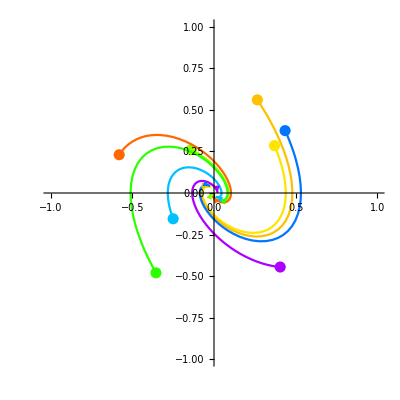
{EquationTrekkerState["tut0.16.","{}",TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>], <>],-Graphics-}

```mathematica
EquationTrekker[u''[t]-(a+d)*u'[t]+(d*a-b*c)*u[t]==0,u,{t,0.1,6.0}]
```

#### Nodal Sink

```mathematica
FindInstance[(a+d)^2 - 4(a*d-b*c)>0 && ((a +d)/2 + Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) * ((a +d)/2 - Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) > 0 && ((a +d)/2 + Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) + ((a +d)/2 - Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) < 0,{a,b,c,d}]
```

{{a→-1,b→1/8,c→-1,d→0}}

```mathematica
a = -1;b = 1/8;c =-1;d = 0;
```

PropertyValue::pvobj: canvas is not an object with properties.

PropertyValue::pvobj: trekPane is not an object with properties.

PropertyValue::poi: -- Message text not found -- (PropertyValue[{canvas,canvasPane,All},Name→trekPane]) (1)

PropertyValue::poi: -- Message text not found -- (PropertyValue[{trekPane,trekController,All},Name→trekController]) (1)

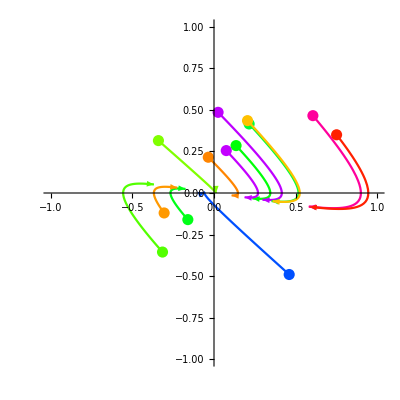
{EquationTrekkerState["u[t]/8ut0.16.","{}",TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>], <>],-Graphics-}

```mathematica
EquationTrekker[u''[t]-(a+d)*u'[t]+(d*a-b*c)*u[t]==0,u,{t,0.1,6.0}]
```

### Spiral Source

```mathematica
FindInstance[(a+d)^2 - 4(a*d-b*c)<0 &&  (a+ d) > 0,{a,b,c,d}]
```

{{a→1,b→1,c→-1,d→0}}

```mathematica
a = 1;b = 1;c =-1;d = 0;
```

PropertyValue::pvobj: canvas is not an object with properties.

PropertyValue::pvobj: trekPane is not an object with properties.

PropertyValue::poi: -- Message text not found -- (PropertyValue[{canvas,canvasPane,All},Name→trekPane]) (1)

PropertyValue::poi: -- Message text not found -- (PropertyValue[{trekPane,trekController,All},Name→trekController]) (1)

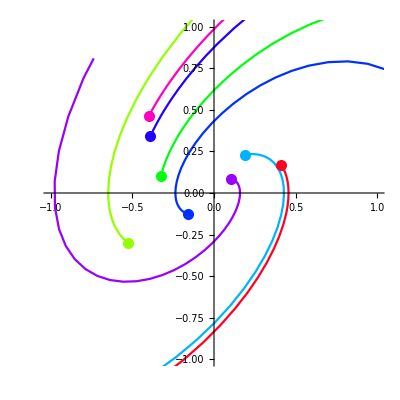
{EquationTrekkerState["tut0.16.","{}",TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>], <>],-Graphics-}

```mathematica
EquationTrekker[u''[t]-(a+d)*u'[t]+(d*a-b*c)*u[t]==0,u,{t,0.1,6.0}]
```

#### Nodal Source:

```mathematica
FindInstance[(a+d)^2 - 4(a*d-b*c)>0 && ((a +d)/2 + Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) * ((a +d)/2 - Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) > 0 && ((a +d)/2 + Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) + ((a +d)/2 - Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) > 0,{a,b,c,d}]
```

{{a→1,b→1/8,c→-1,d→0}}

```mathematica
a = 1;b = 1/8;c =-1;d = 0;
```

PropertyValue::pvobj: canvas is not an object with properties.

PropertyValue::pvobj: trekPane is not an object with properties.

PropertyValue::poi: -- Message text not found -- (PropertyValue[{canvas,canvasPane,All},Name→trekPane]) (1)

PropertyValue::poi: -- Message text not found -- (PropertyValue[{trekPane,trekController,All},Name→trekController]) (1)

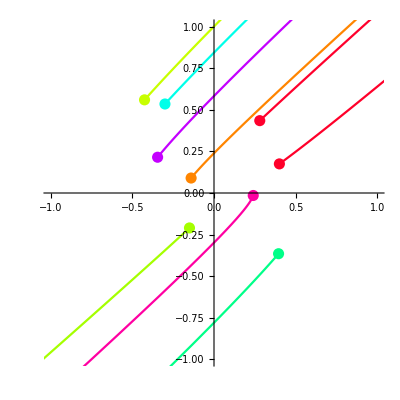
{EquationTrekkerState["u[t]/8ut0.16.","{}",TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>], <>],-Graphics-}

```mathematica
EquationTrekker[u''[t]-(a+d)*u'[t]+(d*a-b*c)*u[t]==0,u,{t,0.1,6.0}]
```

### Saddle

```mathematica
FindInstance[(a+d)^2 - 4(a*d-b*c)>0 && ((a +d)/2 + Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) * ((a +d)/2 - Sqrt[(a+d)^2 - 4(a*d-b*c)]/2) < 0 ,{a,b,c,d}]
```

{{a→-1,b→-1,c→-1,d→0}}

```mathematica
a = -1;b = -1;c =-1;d = 0;
```

PropertyValue::pvobj: canvas is not an object with properties.

PropertyValue::pvobj: trekPane is not an object with properties.

PropertyValue::poi: -- Message text not found -- (PropertyValue[{canvas,canvasPane,All},Name→trekPane]) (1)

PropertyValue::poi: -- Message text not found -- (PropertyValue[{trekPane,trekController,All},Name→trekController]) (1)

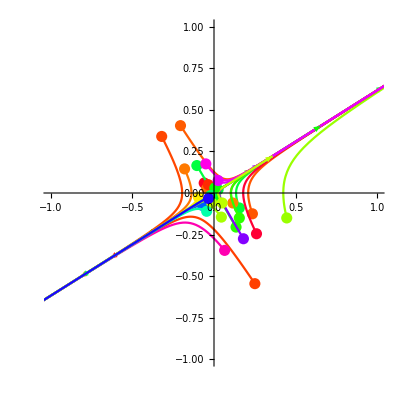
{EquationTrekkerState["-u[t]ut0.16.","{}",TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>], <>],-Graphics-}

```mathematica
EquationTrekker[u''[t]-(a+d)*u'[t]+(d*a-b*c)*u[t]==0,u,{t,0.1,6.0}]
```

### Center

```mathematica
FindInstance[(a+d)^2 - 4(a*d-b*c)<0 && (a + d) == 0,{a,b,c,d}]
```

{{a→0,b→1,c→-1,d→0}}

```mathematica
a = 0;b = 1;c =-1;d = 0;
```

PropertyValue::pvobj: canvas is not an object with properties.

PropertyValue::pvobj: trekPane is not an object with properties.

PropertyValue::poi: -- Message text not found -- (PropertyValue[{canvas,canvasPane,All},Name→trekPane]) (1)

PropertyValue::poi: -- Message text not found -- (PropertyValue[{trekPane,trekController,All},Name→trekController]) (1)

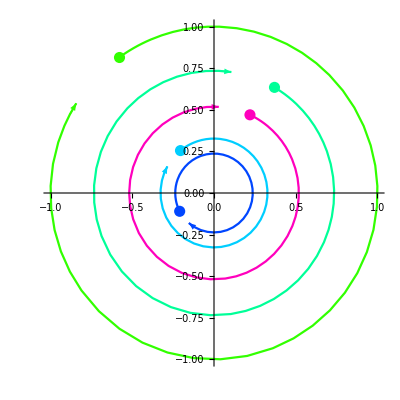
{EquationTrekkerState["tut0.16.","{}",TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>], <>],-Graphics-}

```mathematica
EquationTrekker[u''[t]-(a+d)*u'[t]+(d*a-b*c)*u[t]==0,u,{t,0.1,6.0}]
```

### Degenerate Nodal Source

```mathematica
FindInstance[(a+d)^2 - 4(a*d-b*c)==0 && (a + d) > 0,{a,b,c,d}]
```

{{a→7/8,b→0,c→0,d→7/8}}

```mathematica
a = 7/8;b = 0;c =0;d = 7/8;
```

PropertyValue::pvobj: canvas is not an object with properties.

PropertyValue::pvobj: trekPane is not an object with properties.

PropertyValue::poi: -- Message text not found -- (PropertyValue[{canvas,canvasPane,All},Name→trekPane]) (1)

PropertyValue::poi: -- Message text not found -- (PropertyValue[{trekPane,trekController,All},Name→trekController]) (1)

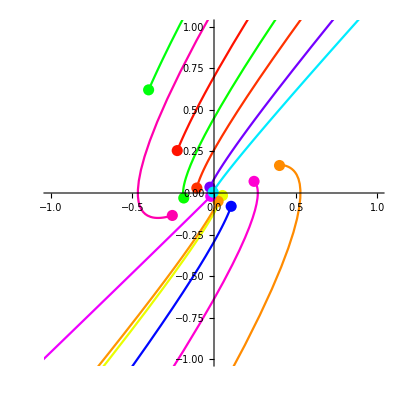
{EquationTrekkerState["(49 u[t])/64ut0.16.","{}",TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>], <>],-Graphics-}

```mathematica
EquationTrekker[u''[t]-(a+d)*u'[t]+(d*a-b*c)*u[t]==0,u,{t,0.1,6.0}]
```

### Degenerate Nodal Sink

```mathematica
FindInstance[(a+d)^2 - 4(a*d-b*c)==0 && (a + d) < 0,{a,b,c,d}]
```

{{a→-1,b→0,c→0,d→-1}}

```mathematica
a = -1;b = 0;c =0;d = -1;
```

PropertyValue::pvobj: canvas is not an object with properties.

PropertyValue::pvobj: trekPane is not an object with properties.

PropertyValue::poi: -- Message text not found -- (PropertyValue[{canvas,canvasPane,All},Name→trekPane]) (1)

PropertyValue::poi: -- Message text not found -- (PropertyValue[{trekPane,trekController,All},Name→trekController]) (1)

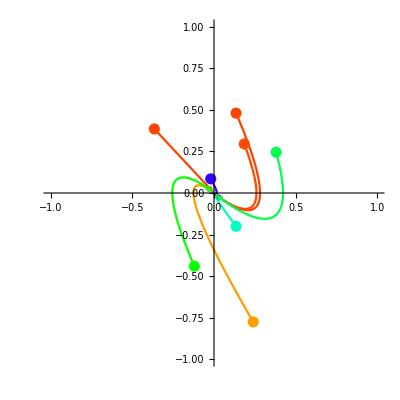
{EquationTrekkerState["tut0.16.","{}",TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>], <>],-Graphics-}

```mathematica
EquationTrekker[u''[t]-(a+d)*u'[t]+(d*a-b*c)*u[t]==0,u,{t,0.1,6.0}]
```

### Unstable Saddle–Node

```mathematica
FindInstance[(a*d-b*c)==0 && (a + d) > 0,{a,b,c,d}]
```

```mathematica
{{a->0,b->0,c->0,d->1}}
```

```mathematica
{{a->0,b->0,c->0,d->1}}
```

```mathematica
a = 0;b = 0;c =0;d = 1;
```

PropertyValue::pvobj: canvas is not an object with properties.

PropertyValue::pvobj: trekPane is not an object with properties.

PropertyValue::poi: -- Message text not found -- (PropertyValue[{canvas,canvasPane,All},Name→trekPane]) (1)

PropertyValue::poi: -- Message text not found -- (PropertyValue[{trekPane,trekController,All},Name→trekController]) (1)

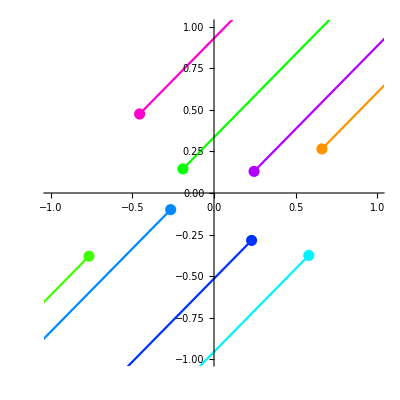
{EquationTrekkerState["u'ut0.16.","{}",TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>], <>],-Graphics-}

```mathematica
EquationTrekker[u''[t]-(a+d)*u'[t]+(d*a-b*c)*u[t]==0,u,{t,0.1,6.0}]
```

### Stable Saddle–Node

```mathematica
FindInstance[(a*d-b*c)==0 && (a + d) < 0,{a,b,c,d}]
```

```mathematica
{{a->0,b->0,c->0,d->-1}}
```

```mathematica
a =  0;b = 0;c =0;d = -1;
```

PropertyValue::pvobj: canvas is not an object with properties.

PropertyValue::pvobj: trekPane is not an object with properties.

PropertyValue::poi: -- Message text not found -- (PropertyValue[{canvas,canvasPane,All},Name→trekPane]) (1)

PropertyValue::poi: -- Message text not found -- (PropertyValue[{trekPane,trekController,All},Name→trekController]) (1)

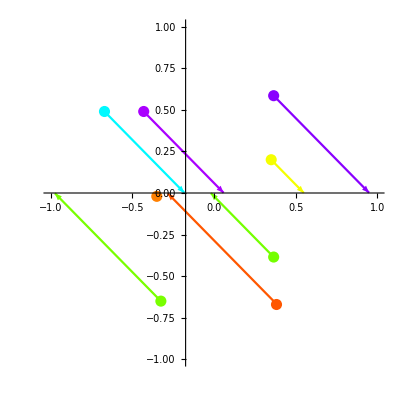
{EquationTrekkerState["u'ut0.16.","{}",TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>]
TrekData["0.1u'", <>], <>],-Graphics-}

```mathematica
EquationTrekker[u''[t]-(a+d)*u'[t]+(d*a-b*c)*u[t]==0,u,{t,0.1,6.0}]
```